# Recamán’s Sequence

Adam Rumpf, 8/25/2018

## Introduction

Recamán’s sequence starts at index n=0 with element a_0=0. To find a_(n+1) given a_n, we either take n steps backward or n steps forward. We go backward if a_n-n is (a) nonnegative and (b) not already part of the sequence. Otherwise we go forward.

Starting from a_0=0, our choices for a_1 are to go backward to -1 or forward to 1. We only allow nonnegative entries, so we take a_1=1. Next we go either 2 steps backward to 0 or 2 steps forward to 3. 0 is already on our list, so we go forward to get a_2=3. For a_3 our choices are 0 or 6, so we take a_3=6. For a_4 our choices are 2 or 10, and since 2 is not yet on our list, we go backwards to a_4=2. The first 10 elements are:

0, 1, 3, 6, 2, 7, 13, 20, 12, 21, ...

The common way to "picture" Recamán's sequence is to draw semicircles on the number line, alternating over/under to connect pairs of consecutive values. Given the values in the sequence, we can generate the shapes with the Circle function.

## Code

### Initialization

```mathematica
(* Generate the first n elements of Recamán's sequence. *)
recaman[n_]:=Module[{out=ConstantArray[-1,n]},
out[[1]]=0;
Do[
If[i-1>out[[i-1]]||MemberQ[out,out[[i-1]]-i+1],
out[[i]]=out[[i-1]]+i-1,
out[[i]]=out[[i-1]]-i+1;
],
{i,2,n}];
out
]
```

```mathematica
(* Given a list of values, draws alternating over/under semicircles on the number line linking consecutive values. *)
rdraw[list_]:=Module[{g={},p=1,c,r},
(* g = list of graphics objects to display
p = parity of current list entry (±1)
c = center of new semicircle
r = radius of new semicircle *)
Do[
c=(list[[i]]+list[[i+1]])/2;
r=Abs[list[[i]]-list[[i+1]]]/2;
g=Append[g,Circle[{c,0},r,If[p>0,{0,Pi},{Pi,2Pi}]]];
p*=-1,
{i,1,Length[list]-1}];
Graphics[g]
]
```

### Demonstration

```mathematica
recaman[20]
```

{0,1,3,6,2,7,13,20,12,21,11,22,10,23,9,24,8,25,43,62}

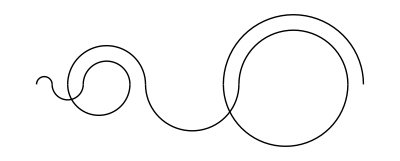

```mathematica
rdraw[recaman[10]]
```

```mathematica
(* Manipulate to generate a long Recamán sequence and animate the drawing process. *)
nmax=100;
rlist=recaman[nmax];
Manipulate[Show[rdraw[rlist[[1;;n]]],PlotRange->{{-1,Max[rlist]+1},{-nmax-1,nmax+1}}],{n,2,nmax,1}]
```